```mathematica
Exit[]
```

```mathematica
$Assumptions=s>0&& S>0 && T>t&&t>0
```

s>0&&S>0&&T>t&&t>0

```mathematica
n[x_]:=Exp[-x^2/2]/Sqrt[2 π]
```

```mathematica
d[t_]:=(Log[S/K]+s^2/2(T-t))/s/Sqrt[T-t];
```

```mathematica
th[t_]:=-s S n[d[t]]/Sqrt[T-t]/2
```

```mathematica
Integrate[th[t]/K^2,{K,0,Infinity}]
```

-s^2/2

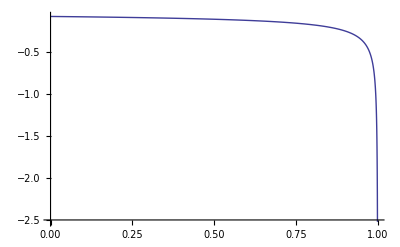

```mathematica
T=1;s=0.2;K=1;Plot[th[x],{x,0,0.999},PlotRange->All]
```

```mathematica
th[0.99999]//N
```

-3.67331×10^-53

```mathematica
S=K
```

K

```mathematica
th[t]
```

-(ⅇ^(-1/8 s^2 (-t+T)) K s)/(√(2 π) √(-t+T))

```mathematica
dn=D[n[d],t]
```

(ⅇ^(-((1/2 s^2 (-t+T)+Log[S/K])^2)/(2 s^2 (-t+T))) ((1/2 s^2 (-t+T)+Log[S/K])/(2 (-t+T))-((1/2 s^2 (-t+T)+Log[S/K])^2)/(2 s^2 (-t+T)^2)))/(√(2 π))

```mathematica
th=Simplify[-s S 2  Sqrt[T-t] dn]
```

-(ⅇ^(((s^2 (t-T)-2 Log[S/K])^2)/(8 s^2 (t-T))) S (s^4 (t-T)^2-4 Log[S/K]^2))/(4 √(2 π) s (-t+T)^(3/2))

```mathematica
(ⅇ^(((s^2 (t-T)-2 Log[S/K])^2)/(8 s^2 (t-T))) S 4 Log[S/K]^2)/(4 √(2 π) s (-t+T)^(3/2))
```

```mathematica
Simplify[D[ⅇ^((2 Log[S/K])^2/(8 s^2 (t-T))) S 4 Log[S/K]^2,t]/D[4 √(2 π) s (-t+T)^(3/2)]]
```

-(ⅇ^(Log[S/K]^2/(2 s^2 (t-T))) S Log[S/K]^4)/(2 √(2 π) s^3 (-t+T)^(7/2))

```mathematica
Simplify[D[Exp[-1/x],x]/D[Sqrt[x],x]]
```

(2 ⅇ^(-1/x))/x^(3/2)

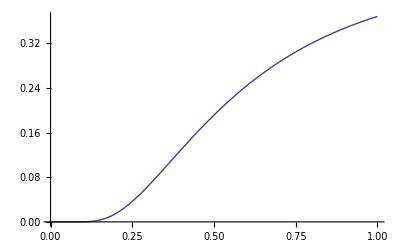

```mathematica
Plot[Exp[-1/x]/Sqrt[x],{x,0,1}]
```

```mathematica
D[Sqrt[y],y]
```

1/(2 √y)

```mathematica
Limit[th[t],t->T]
```

Limit[-ⅇ^(-((1/2 s^2 (-t+T)+Log[S/K])^2)/(2 s^2 (-t+T))) √(2/π) s S √(-t+T) ((1/2 s^2 (-t+T)+Log[S/K])/(2 (-t+T))-((1/2 s^2 (-t+T)+Log[S/K])^2)/(2 s^2 (-t+T)^2)),t→T]

```mathematica
D[Sqrt[t],t]
```

1/(2 √t)

```mathematica
D[d,t]
```

-s/(2 √(-t+T))+(1/2 s^2 (-t+T)+Log[S/K])/(2 s (-t+T)^(3/2))